ClearAll

Derived Lagrangian

{{0.201064},{0.247058},{0.283347},{0.311155},{0.332474},{0.348821},{0.361354},{0.370966},{0.37833},{0.383966},{0.388274},{0.391555},{0.394062},{0.395986},{0.39746},{0.398579},{0.399425},{0.400064},{0.40053},{0.400857},{0.401096},{0.401289},{0.401448},{0.401576},{0.401678},{0.401769},{0.401849},{0.401909},{0.401959},{0.402013},{0.40206},{0.402078},{0.402057},{0.401967},{0.401849},{0.401782},{0.401762},{0.401774},{0.401798},{0.401821},{0.401859},{0.40192},{0.401984},{0.402028},{0.402035},{0.401991},{0.401925}}

Placed::labpos: {0.6} is not a valid position for the placement of labels.

-Graphics-

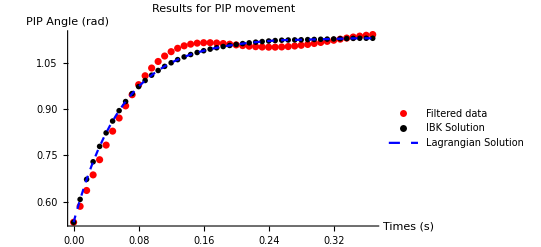

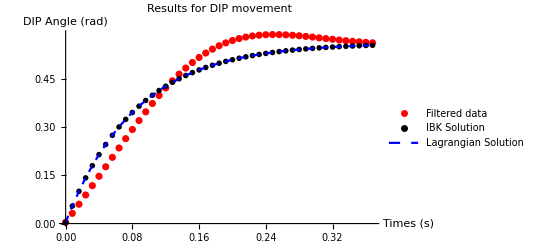

-Graphics-

Derived Lagrangian

Part::pkspec1: The expression {0.201064,0.232164,0.2624,0.290948,0.317088,0.340263,0.360111,0.376478,0.389418,0.399163,«37»} cannot be used as a part specification.

Length⟦{0.201064,0.232164,0.2624,0.290948,0.317088,0.340263,0.360111,0.376478,0.389418,0.399163,0.406083,0.410649,0.413378,0.414794,0.415381,0.415543,0.415573,0.415637,0.415777,0.415934,0.415979,0.415766,0.415174,0.414141,0.412683,0.410888,0.408902,0.406894,0.405026,0.403425,0.402158,0.40123,0.400582,0.400114,0.399705,0.399247,0.398673,0.397973,0.397206,0.39649,0.395984,0.395851,0.396231,0.397199,0.398749,0.400782,0.403125}⟧

```mathematica
ClearAll
(*Model Parameters. These must be defined beforehand*)

L1=44.13*10^-3; (*Proximal Segment length in meters*)
L2=28.01*10^-3; (*Middle Segment length in meters*)
L3=26.31*10^-3; (*Distal Segment length in meters*)
rho=1.16*10^3 ;(*Human hand density in kg/m^3*)
R1=9.86*10^-3; (*Proximal Segment radius in meters*)
R2=8.525*10^-3;(*Middle Segment radius in meters*)
R3=7.82*10^-3;(*Distal Segment radius in meters*)
m1=Pi*rho*R1^2*L1; (*Proximal Segment mass in Kg*)
m2=Pi*rho*R2^2*L2;(*Middle Segment mass in Kg*)
m3=Pi*rho*R3^2*L3;(*Distal Segment mass in Kg*)
I1=m1*(R1^2/4+L1^2/12);(*Proximal Segment moment of inertia about its COM in Kg*m^2*)
I2=m2*(R2^2/4+L2^2/12);(*Middle Segment moment of inertia about its COM in Kg*m^2*)
I3=m3*(R3^2/4+L3^2/12); (*Distal Segment moment of inertia about its COM in Kg*m^2*)
K1=9.144692854; (*Proximal Segment torsional spring constant determined from optimisation N*m/rad*)
K2=5.124550619;(*Middle Segment torsional spring constant determined from optimisation N*m/rad*)
K3=9.908332147;(*Distal Segment torsional spring constant determined from optimisation N*m/rad*)
b1=0.277430345;(*Proximal Segment torsional spring constant determined from optimisation N*m*s/rad*)
b2=0.314324434;(*Middle Segment torsional spring constant determined from optimisation N*m*s/rad*)
b3=0.837228995;(*Distal Segment torsional damper constant determined from optimisation N*m*s/rad*)
(*Muscle moment scaling parameters as determined from IBK solution*)
redcMCP=0.137721699;
rfdpMCP=0.13841923;
rfdsMCP=0.139049285;
redcPIP=0.701845852;
rfdpPIP=0.690272427;
rfdsPIP=0.696480248;
redcDIP=0.101906797;
rfdpDIP=0.101906752;

(*Import MATLAB data*)
U=Import["C:\\Users\\u1857308\\OneDrive - University of Warwick\\PhD\\Hand Trials\\Results\\Cylindrical Grasp\\P1\\Trial_digit2_Par_1_Thelen_trial3.csv","csv"];
(*Experiment time*)
tim=U[[All,9]];

(*Cubic spline interpolation of Muscle moment data*)
EDCMCP=Interpolation[Transpose[{tim,U[[All,1]]}]];
FDPMCP=Interpolation[Transpose[{tim,U[[All,2]]}]];
FDSMCP=Interpolation[Transpose[{tim,U[[All,3]]}]];
EDCPIP=Interpolation[Transpose[{tim,U[[All,4]]}]];
FDPPIP=Interpolation[Transpose[{tim,U[[All,5]]}]];
FDSPIP=Interpolation[Transpose[{tim,U[[All,6]]}]];
EDCDIP=Interpolation[Transpose[{tim,U[[All,7]]}]];
FDPDIP=Interpolation[Transpose[{tim,U[[All,8]]}]];

(*Filtered MoCap data*)
th1f=U[[All,10]];
th2f=U[[All,12]];
th3f=U[[All,14]];
th1eq=Last[th1f]; (*Proximal Segment equilibrium angle in rad*)
th2eq=Last[th2f];(*Middle Segment equilibrium angle in rad*)
th3eq=Last[th3f];(*Distal Segment equilibrium angle in rad*)


Derived Lagrangian
(*Triple pendulum Lagrangian with no abduction movement*)
x1[t]=-L1/2*Cos[th1[t]];
y1[t]=-L1/2*Sin[th1[t]];
x2[t]=-(L1*Cos[th1[t]]+L2/2*Cos[th2[t]]);
y2[t]=-(L1*Sin[th1[t]]+L2/2*Sin[th2[t]]);
x3[t]=-(L1*Cos[th1[t]]+L2*Cos[th2[t]]+L3/2*Cos[th3[t]]);
y3[t]=-(L1*Sin[th1[t]]+L2*Sin[th2[t]]+L3/2*Sin[th3[t]]);

(*Translational part for Parallel axis Theorem*)
r1[t]=D[x1[t],t]^2+D[y1[t],t]^2;
Simplify[r1[t]];
r2[t]=D[x2[t],t]^2+D[y2[t],t]^2;
Simplify[Expand[r2[t]]];
r3[t]=D[x3[t],t]^2+D[y3[t],t]^2;
Simplify[Expand[r3[t]]];
K1a=1/2*(m1*r1[t]+m2*r2[t]+m3*r3[t]);

(*Rotational Kinetic Energy*)
T=1/2*(I1*(th1'[t]^2)+I2*(th2'[t]^2)+I3*(th3'[t]^2));
Kt=K1a+T//FullSimplify;

(*Spring Potential Energy*)
Vspr=K1/2*(th1[t]-th1eq)^2+K2/2*(th2[t]-th2eq)^2+K3/2*(th3[t]-th3eq)^2;
V=Vspr;

(*Lagrangian Function*)
L=Kt-V;

(*Euler-Lagrange equations*)
a=D[D[L,th1'[t]],t]-D[L,th1[t]]+b1*th1'[t];
a//FullSimplify;
b=D[D[L,th2'[t]],t]-D[L,th2[t]]+b2*th2'[t];
b//FullSimplify;
c=D[D[L,th3'[t]],t]-D[L,th3[t]]+b3*th3'[t];
c//FullSimplify;



(*IBK solution data*)
Y1=U[[All,15]];
Y2=U[[All,16]];
Y3=U[[All,17]];

(*Input functions generation*)
u1[t_]=redcMCP*EDCMCP[t]+rfdpMCP*FDPMCP[t]+rfdsMCP*FDSMCP[t];
u2[t_]=redcPIP*EDCPIP[t]+rfdpPIP*FDPPIP[t]+rfdsPIP*FDSPIP[t];
u3[t_]=redcDIP*EDCDIP[t]+rfdpDIP*FDPDIP[t];

(*Initial conditions*)
init={th1[0]==th1f[[1]],th1'[0]==0,th2[0]==th2f[[1]],th2'[0]==0,th3[0]==th3f[[1]],th3'[0]==0};

(*Differential equations*)
eqn={a==u1[t],b==u2[t],c==u3[t]};

(*Solving Differential Equations*)
s=NDSolve[{eqn,init},{th1[t],th1'[t],th2[t],th2'[t],th3[t],th3'[t]},{t,tim[[1]],Last[tim]},Method->"StiffnessSwitching",MaxStepSize->10^-4];


timePoints = N[Range[tim[[1]],Last[tim],1/125]];
th1S=th1[t]/.s;
th1Values = N[Table[Flatten[Evaluate[th1S/. t -> tval]], {tval, timePoints}]];


(*MCP results plot*)
ListLinePlot[{Transpose[{tim,th1f}],Transpose[{tim,Y1}],Transpose[{timePoints,th1Values}]},PlotRange->All,Frame->True,PlotLegends->Placed[{"Filtered data","IBK Solution","Lagrangian Solution"},{0.6}],PlotLabel->"Results for MCP movement",PlotRange->All,FrameLabel->{"Times (s)","MCP Angle (rad)"},PlotStyle->{Automatic, Dashed, Circle}]

(*PIP Results plot*)
Show[
ListPlot[Transpose[{tim,th2f}],PlotStyle->Red,PlotRange->All,PlotLabel->"Data",PlotLegends->{"Filtered data"}],ListPlot[Transpose[{tim,Y2}],PlotStyle->{Black,PointSize[0.01]},PlotRange->All,PlotLabel->"Data",PlotLegends->{"IBK Solution"}],
Plot[{Evaluate[th2[t]/.s]},{t,tim[[1]],Last[tim]},PlotStyle->{Dashed,Blue},PlotLegends->{"Lagrangian Solution"}],PlotLabel->"Results for PIP movement",PlotRange->All,AxesLabel->{"Times (s)","PIP Angle (rad)"}]

(*DIP Results Plot*)
Show[
ListPlot[Transpose[{tim,th3f}],PlotStyle->Red,PlotRange->All,PlotLabel->"Data",PlotLegends->{"Filtered data"}],ListPlot[Transpose[{tim,Y3}],PlotStyle->{Black,PointSize[0.01]}, PlotRange->All,PlotLabel->"Data",PlotLegends->{"IBK Solution"}],
Plot[{Evaluate[th3[t]/.s]},{t,tim[[1]],Last[tim]},PlotStyle->{Dashed,Blue},PlotLegends->{"Lagrangian Solution"}],PlotLabel->"Results for DIP movement",PlotRange->All,AxesLabel->{"Times (s)","DIP Angle (rad)"}]


(*MCP Difference plot*)
Show[
ListPlot[Transpose[{tim,th3f}],PlotStyle->Red,PlotRange->All,PlotLabel->"Data",PlotLegends->{"Filtered data"}],ListPlot[Transpose[{tim,Y3}],PlotStyle->{Black,PointSize[0.01]}, PlotRange->All,PlotLabel->"Data",PlotLegends->{"IBK Solution"}],
Plot[{Evaluate[th3[t]/.s]},{t,tim[[1]],Last[tim]},PlotStyle->{Dashed,Blue},PlotLegends->{"Lagrangian Solution"}],PlotLabel->"Results for DIP movement",PlotRange->All,AxesLabel->{"Times (s)","DIP Angle (rad)"}]

n=2000;
datath1s=Table[Flatten[{t,Evaluate[th1[t]/.s]}],{t,tim[[1]],Last[tim],Last[tim]/(n-1)}];
Export["Th1S.csv",datath1s,"CSV"];
datath1s=Table[Flatten[{t,Evaluate[th2[t]/.s]}],{t,tim[[1]],Last[tim],Last[tim]/(n-1)}];
Export["Th2S.csv",datath1s,"CSV"];
datath1s=Table[Flatten[{t,Evaluate[th3[t]/.s]}],{t,tim[[1]],Last[tim],Last[tim]/(n-1)}];
Export["Th3S.csv",datath1s,"CSV"];
```

```mathematica
ClearAll
```

ClearAll

```mathematica
th1[t]/.s
```

{InterpolatingFunction[…][t]}

```mathematica
Range[tim[[1]],Last[tim],150]
```

{0}

```mathematica
ListLinePot[Transpose[{timePoints,th1Values}],PlotRange->All]
```

ListLinePot[{{0,{0.201064}},{1/125,{0.247058}},{2/125,{0.283347}},{3/125,{0.311155}},{4/125,{0.332474}},{1/25,{0.348821}},{6/125,{0.361354}},{7/125,{0.370966}},{8/125,{0.37833}},{9/125,{0.383966}},{2/25,{0.388274}},{11/125,{0.391555}},{12/125,{0.394062}},{13/125,{0.395986}},{14/125,{0.39746}},{3/25,{0.398579}},{16/125,{0.399425}},{17/125,{0.400064}},{18/125,{0.40053}},{19/125,{0.400857}},{4/25,{0.401096}},{21/125,{0.401289}},{22/125,{0.401448}},{23/125,{0.401576}},{24/125,{0.401678}},{1/5,{0.401769}},{26/125,{0.401849}},{27/125,{0.401909}},{28/125,{0.401959}},{29/125,{0.402013}},{6/25,{0.40206}},{31/125,{0.402078}},{32/125,{0.402057}},{33/125,{0.401967}},{34/125,{0.401849}},{7/25,{0.401782}},{36/125,{0.401762}},{37/125,{0.401774}},{38/125,{0.401798}},{39/125,{0.401821}},{8/25,{0.401859}},{41/125,{0.40192}},{42/125,{0.401984}},{43/125,{0.402028}},{44/125,{0.402035}},{9/25,{0.401991}},{46/125,{0.401925}}},PlotRange→All]

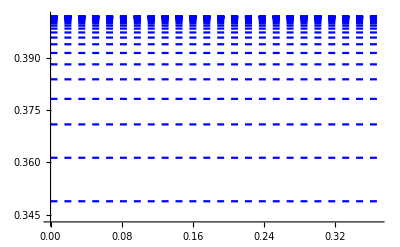

```mathematica
Plot[Transpose[th1Values],{t,tim[[1]],Last[tim]},PlotStyle->{Dashed,Blue}]
```

```mathematica
Last[th1f]
```

0.403125